```mathematica
ClearAll["Global`*"]
```

## Constant height test

```mathematica
g=9.80655;
m=.056+1.518;
```

```mathematica
a[α_,β_,γ_]:={g*m*Sec[β]*Sec[γ]*(Cos[α]*Cos[γ]*Sin[β]+Sin[α]*Sin[γ]),g*m*Sec[β]*Sec[γ]*(Cos[γ]*Sin[α]*Sin[β]-Cos[α]*Sin[γ]),0}/m
```

```mathematica
(*soln=NDSolve[{r''[t]==a[0,0,Pi/6],
r[0]=={0,0,0},
r'[0]=={0,0,0}},r[t],{t,0,1.0}]
rsol[t_]=soln[[1,1,2]]
ParametricPlot3D[{rsol[t]rsol'[t]},{t,0,1.0}]*)
```

```mathematica
t0=0;
dt=1/20;
table={};
vtable={};
rtable={};
For[α=0,α<π/2,α=α+π/6,
For[β=0,β<π/2,β=β+π/6,
For[γ=0,γ<π/2,γ=γ+π/6,
soln=NDSolve[{r''[s]==a[α,β,γ],
r[0]=={0,0,0},
r'[0]=={0,0,0}},r[s],{s,0,1.0}];
rsol[s_]=soln[[1,1,2]];
For[t=0,t<1.0,t=t+dt,
(*Print[{α,β,γ,N[t]}];*)
rfunc[s_]=Integrate[a[α,β,γ],s,s];
rint=rfunc[t];
AppendTo[rtable,{t,rint[[3]]}];
(*Print[r];*)
vfunc[s_]=Integrate[a[α,β,γ],s];
vint=vfunc[t];
AppendTo[vtable,{N[t],vint[[3]]}];
AppendTo[table,{α,β,γ,N[t],vint,rsol'[t],rint,rsol[t]}]
]
]
]
]
```

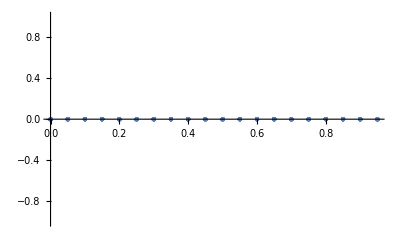

0 |   0 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 |   0 |  1.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
  0 |   0 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
 0.0
  0 |  0.0
 0.0
 0.0
  0 |   0 | π/6 |  0.1 |  0.0
-0.3
 0.0 |  0.0
-0.3
 0.0 |   0
-0.0
  0 |  0.0
-0.0
 0.0
  0 |   0 | π/6 |  0.1 |  0.0
-0.6
 0.0 |  0.0
-0.6
 0.0 |   0
-0.0
  0 |  0.0
-0.0
 0.0
  0 |   0 | π/6 |  0.2 |  0.0
-0.8
 0.0 |  0.0
-0.8
 0.0 |   0
-0.1
  0 |  0.0
-0.1
 0.0
  0 |   0 | π/6 |  0.2 |  0.0
-1.1
 0.0 |  0.0
-1.1
 0.0 |   0
-0.1
  0 |  0.0
-0.1
 0.0
  0 |   0 | π/6 |  0.3 |  0.0
-1.4
 0.0 |  0.0
-1.4
 0.0 |   0
-0.2
  0 |  0.0
-0.2
 0.0
  0 |   0 | π/6 |  0.3 |  0.0
-1.7
 0.0 |  0.0
-1.7
 0.0 |   0
-0.3
  0 |  0.0
-0.3
 0.0
  0 |   0 | π/6 |  0.4 |  0.0
-2.0
 0.0 |  0.0
-2.0
 0.0 |   0
-0.3
  0 |  0.0
-0.3
 0.0
  0 |   0 | π/6 |  0.4 |  0.0
-2.3
 0.0 |  0.0
-2.3
 0.0 |   0
-0.5
  0 |  0.0
-0.5
 0.0
  0 |   0 | π/6 |  0.5 |  0.0
-2.5
 0.0 |  0.0
-2.5
 0.0 |   0
-0.6
  0 |  0.0
-0.6
 0.0
  0 |   0 | π/6 |  0.5 |  0.0
-2.8
 0.0 |  0.0
-2.8
 0.0 |   0
-0.7
  0 |  0.0
-0.7
 0.0
  0 |   0 | π/6 |  0.6 |  0.0
-3.1
 0.0 |  0.0
-3.1
 0.0 |   0
-0.9
  0 |  0.0
-0.9
 0.0
  0 |   0 | π/6 |  0.6 |  0.0
-3.4
 0.0 |  0.0
-3.4
 0.0 |   0
-1.0
  0 |  0.0
-1.0
 0.0
  0 |   0 | π/6 |  0.7 |  0.0
-3.7
 0.0 |  0.0
-3.7
 0.0 |   0
-1.2
  0 |  0.0
-1.2
 0.0
  0 |   0 | π/6 |  0.7 |  0.0
-4.0
 0.0 |  0.0
-4.0
 0.0 |   0
-1.4
  0 |  0.0
-1.4
 0.0
  0 |   0 | π/6 |  0.8 |  0.0
-4.2
 0.0 |  0.0
-4.2
 0.0 |   0
-1.6
  0 |  0.0
-1.6
 0.0
  0 |   0 | π/6 |  0.8 |  0.0
-4.5
 0.0 |  0.0
-4.5
 0.0 |   0
-1.8
  0 |  0.0
-1.8
 0.0
  0 |   0 | π/6 |  0.9 |  0.0
-4.8
 0.0 |  0.0
-4.8
 0.0 |   0
-2.0
  0 |  0.0
-2.0
 0.0
  0 |   0 | π/6 |  0.9 |  0.0
-5.1
 0.0 |  0.0
-5.1
 0.0 |   0
-2.3
  0 |  0.0
-2.3
 0.0
  0 |   0 | π/6 |  1.0 |  0.0
-5.4
 0.0 |  0.0
-5.4
 0.0 |   0
-2.6
  0 |  0.0
-2.6
 0.0
  0 |   0 | π/3 |  0.0 |  0.0
 0.0
 0.0 |  0.0
-5.4×10^-20
 0.0 |   0
 0.0
  0 |  0.0
 0.0
 0.0
  0 |   0 | π/3 |  0.1 |  0.0
-0.8
 0.0 |  0.0
-0.8
 0.0 |   0
-0.0
  0 |  0.0
-0.0
 0.0
  0 |   0 | π/3 |  0.1 |  0.0
-1.7
 0.0 |  0.0
-1.7
 0.0 |   0
-0.1
  0 |  0.0
-0.1
 0.0
  0 |   0 | π/3 |  0.2 |  0.0
-2.5
 0.0 |  0.0
-2.5
 0.0 |   0
-0.2
  0 |  0.0
-0.2
 0.0
  0 |   0 | π/3 |  0.2 |  0.0
-3.4
 0.0 |  0.0
-3.4
 0.0 |   0
-0.3
  0 |  0.0
-0.3
 0.0
  0 |   0 | π/3 |  0.3 |  0.0
-4.2
 0.0 |  0.0
-4.2
 0.0 |   0
-0.5
  0 |  0.0
-0.5
 0.0
  0 |   0 | π/3 |  0.3 |  0.0
-5.1
 0.0 |  0.0
-5.1
 0.0 |   0
-0.8
  0 |  0.0
-0.8
 0.0
  0 |   0 | π/3 |  0.4 |  0.0
-5.9
 0.0 |  0.0
-5.9
 0.0 |   0
-1.0
  0 |  0.0
-1.0
 0.0
  0 |   0 | π/3 |  0.4 |  0.0
-6.8
 0.0 |  0.0
-6.8
 0.0 |   0
-1.4
  0 |  0.0
-1.4
 0.0
  0 |   0 | π/3 |  0.5 |  0.0
-7.6
 0.0 |  0.0
-7.6
 0.0 |   0
-1.7
  0 |  0.0
-1.7
 0.0
  0 |   0 | π/3 |  0.5 |  0.0
-8.5
 0.0 |  0.0
-8.5
 0.0 |   0
-2.1
  0 |  0.0
-2.1
 0.0
  0 |   0 | π/3 |  0.6 |  0.0
-9.3
 0.0 |  0.0
-9.3
 0.0 |   0
-2.6
  0 |  0.0
-2.6
 0.0
  0 |   0 | π/3 |  0.6 |  0.0
-10.0
 0.0 |  0.0
-10.0
 0.0 |   0
-3.1
  0 |  0.0
-3.1
 0.0
  0 |   0 | π/3 |  0.7 |  0.0
-11.0
 0.0 |  0.0
-11.0
 0.0 |   0
-3.6
  0 |  0.0
-3.6
 0.0
  0 |   0 | π/3 |  0.7 |  0.0
-12.0
 0.0 |  0.0
-12.0
 0.0 |   0
-4.2
  0 |  0.0
-4.2
 0.0
  0 |   0 | π/3 |  0.8 |  0.0
-13.0
 0.0 |  0.0
-13.0
 0.0 |   0
-4.8
  0 |  0.0
-4.8
 0.0
  0 |   0 | π/3 |  0.8 |  0.0
-14.0
 0.0 |  0.0
-14.0
 0.0 |   0
-5.4
  0 |  0.0
-5.4
 0.0
  0 |   0 | π/3 |  0.9 |  0.0
-14.0
 0.0 |  0.0
-14.0
 0.0 |   0
-6.1
  0 |  0.0
-6.1
 0.0
  0 |   0 | π/3 |  0.9 |  0.0
-15.0
 0.0 |  0.0
-15.0
 0.0 |   0
-6.9
  0 |  0.0
-6.9
 0.0
  0 |   0 | π/3 |  1.0 |  0.0
-16.0
 0.0 |  0.0
-16.0
 0.0 |   0
-7.7
  0 |  0.0
-7.7
 0.0
  0 | π/6 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |  0.0
  0
  0 |  0.0
 0.0
 0.0
  0 | π/6 |   0 |  0.1 |  0.3
 0.0
 0.0 |  0.3
 0.0
 0.0 |  0.0
  0
  0 |  0.0
 0.0
 0.0
  0 | π/6 |   0 |  0.1 |  0.6
 0.0
 0.0 |  0.6
 0.0
 0.0 |  0.0
  0
  0 |  0.0
 0.0
 0.0
  0 | π/6 |   0 |  0.2 |  0.8
 0.0
 0.0 |  0.8
 0.0
 0.0 |  0.1
  0
  0 |  0.1
 0.0
 0.0
  0 | π/6 |   0 |  0.2 |  1.1
 0.0
 0.0 |  1.1
 0.0
 0.0 |  0.1
  0
  0 |  0.1
 0.0
 0.0
  0 | π/6 |   0 |  0.3 |  1.4
 0.0
 0.0 |  1.4
 0.0
 0.0 |  0.2
  0
  0 |  0.2
 0.0
 0.0
  0 | π/6 |   0 |  0.3 |  1.7
 0.0
 0.0 |  1.7
 0.0
 0.0 |  0.3
  0
  0 |  0.3
 0.0
 0.0
  0 | π/6 |   0 |  0.4 |  2.0
 0.0
 0.0 |  2.0
 0.0
 0.0 |  0.3
  0
  0 |  0.3
 0.0
 0.0
  0 | π/6 |   0 |  0.4 |  2.3
 0.0
 0.0 |  2.3
 0.0
 0.0 |  0.5
  0
  0 |  0.5
 0.0
 0.0
  0 | π/6 |   0 |  0.5 |  2.5
 0.0
 0.0 |  2.5
 0.0
 0.0 |  0.6
  0
  0 |  0.6
 0.0
 0.0
  0 | π/6 |   0 |  0.5 |  2.8
 0.0
 0.0 |  2.8
 0.0
 0.0 |  0.7
  0
  0 |  0.7
 0.0
 0.0
  0 | π/6 |   0 |  0.6 |  3.1
 0.0
 0.0 |  3.1
 0.0
 0.0 |  0.9
  0
  0 |  0.9
 0.0
 0.0
  0 | π/6 |   0 |  0.6 |  3.4
 0.0
 0.0 |  3.4
 0.0
 0.0 |  1.0
  0
  0 |  1.0
 0.0
 0.0
  0 | π/6 |   0 |  0.7 |  3.7
 0.0
 0.0 |  3.7
 0.0
 0.0 |  1.2
  0
  0 |  1.2
 0.0
 0.0
  0 | π/6 |   0 |  0.7 |  4.0
 0.0
 0.0 |  4.0
 0.0
 0.0 |  1.4
  0
  0 |  1.4
 0.0
 0.0
  0 | π/6 |   0 |  0.8 |  4.2
 0.0
 0.0 |  4.2
 0.0
 0.0 |  1.6
  0
  0 |  1.6
 0.0
 0.0
  0 | π/6 |   0 |  0.8 |  4.5
 0.0
 0.0 |  4.5
 0.0
 0.0 |  1.8
  0
  0 |  1.8
 0.0
 0.0
  0 | π/6 |   0 |  0.9 |  4.8
 0.0
 0.0 |  4.8
 0.0
 0.0 |  2.0
  0
  0 |  2.0
 0.0
 0.0
  0 | π/6 |   0 |  0.9 |  5.1
 0.0
 0.0 |  5.1
 0.0
 0.0 |  2.3
  0
  0 |  2.3
 0.0
 0.0
  0 | π/6 |   0 |  1.0 |  5.4
 0.0
 0.0 |  5.4
 0.0
 0.0 |  2.6
  0
  0 |  2.6
 0.0
 0.0
  0 | π/6 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  0.0
-2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
  0 | π/6 | π/6 |  0.1 |  0.3
-0.3
 0.0 |  0.3
-0.3
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
  0 | π/6 | π/6 |  0.1 |  0.6
-0.7
 0.0 |  0.6
-0.7
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
  0 | π/6 | π/6 |  0.2 |  0.8
-1.0
 0.0 |  0.8
-1.0
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
  0 | π/6 | π/6 |  0.2 |  1.1
-1.3
 0.0 |  1.1
-1.3
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
  0 | π/6 | π/6 |  0.3 |  1.4
-1.6
 0.0 |  1.4
-1.6
 0.0 |  0.2
-0.2
  0 |  0.2
-0.2
 0.0
  0 | π/6 | π/6 |  0.3 |  1.7
-2.0
 0.0 |  1.7
-2.0
 0.0 |  0.3
-0.3
  0 |  0.3
-0.3
 0.0
  0 | π/6 | π/6 |  0.4 |  2.0
-2.3
 0.0 |  2.0
-2.3
 0.0 |  0.3
-0.4
  0 |  0.3
-0.4
 0.0
  0 | π/6 | π/6 |  0.4 |  2.3
-2.6
 0.0 |  2.3
-2.6
 0.0 |  0.5
-0.5
  0 |  0.5
-0.5
 0.0
  0 | π/6 | π/6 |  0.5 |  2.5
-2.9
 0.0 |  2.5
-2.9
 0.0 |  0.6
-0.7
  0 |  0.6
-0.7
 0.0
  0 | π/6 | π/6 |  0.5 |  2.8
-3.3
 0.0 |  2.8
-3.3
 0.0 |  0.7
-0.8
  0 |  0.7
-0.8
 0.0
  0 | π/6 | π/6 |  0.6 |  3.1
-3.6
 0.0 |  3.1
-3.6
 0.0 |  0.9
-1.0
  0 |  0.9
-1.0
 0.0
  0 | π/6 | π/6 |  0.6 |  3.4
-3.9
 0.0 |  3.4
-3.9
 0.0 |  1.0
-1.2
  0 |  1.0
-1.2
 0.0
  0 | π/6 | π/6 |  0.7 |  3.7
-4.2
 0.0 |  3.7
-4.2
 0.0 |  1.2
-1.4
  0 |  1.2
-1.4
 0.0
  0 | π/6 | π/6 |  0.7 |  4.0
-4.6
 0.0 |  4.0
-4.6
 0.0 |  1.4
-1.6
  0 |  1.4
-1.6
 0.0
  0 | π/6 | π/6 |  0.8 |  4.2
-4.9
 0.0 |  4.2
-4.9
 0.0 |  1.6
-1.8
  0 |  1.6
-1.8
 0.0
  0 | π/6 | π/6 |  0.8 |  4.5
-5.2
 0.0 |  4.5
-5.2
 0.0 |  1.8
-2.1
  0 |  1.8
-2.1
 0.0
  0 | π/6 | π/6 |  0.9 |  4.8
-5.6
 0.0 |  4.8
-5.6
 0.0 |  2.0
-2.4
  0 |  2.0
-2.4
 0.0
  0 | π/6 | π/6 |  0.9 |  5.1
-5.9
 0.0 |  5.1
-5.9
 0.0 |  2.3
-2.6
  0 |  2.3
-2.6
 0.0
  0 | π/6 | π/6 |  1.0 |  5.4
-6.2
 0.0 |  5.4
-6.2
 0.0 |  2.6
-3.0
  0 |  2.6
-3.0
 0.0
  0 | π/6 | π/3 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 5.4×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
  0 | π/6 | π/3 |  0.1 |  0.3
-1.0
 0.0 |  0.3
-1.0
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
  0 | π/6 | π/3 |  0.1 |  0.6
-2.0
 0.0 |  0.6
-2.0
 0.0 |  0.0
-0.1
  0 |  0.0
-0.1
 0.0
  0 | π/6 | π/3 |  0.2 |  0.8
-2.9
 0.0 |  0.8
-2.9
 0.0 |  0.1
-0.2
  0 |  0.1
-0.2
 0.0
  0 | π/6 | π/3 |  0.2 |  1.1
-3.9
 0.0 |  1.1
-3.9
 0.0 |  0.1
-0.4
  0 |  0.1
-0.4
 0.0
  0 | π/6 | π/3 |  0.3 |  1.4
-4.9
 0.0 |  1.4
-4.9
 0.0 |  0.2
-0.6
  0 |  0.2
-0.6
 0.0
  0 | π/6 | π/3 |  0.3 |  1.7
-5.9
 0.0 |  1.7
-5.9
 0.0 |  0.3
-0.9
  0 |  0.3
-0.9
 0.0
  0 | π/6 | π/3 |  0.4 |  2.0
-6.9
 0.0 |  2.0
-6.9
 0.0 |  0.3
-1.2
  0 |  0.3
-1.2
 0.0
  0 | π/6 | π/3 |  0.4 |  2.3
-7.8
 0.0 |  2.3
-7.8
 0.0 |  0.5
-1.6
  0 |  0.5
-1.6
 0.0
  0 | π/6 | π/3 |  0.5 |  2.5
-8.8
 0.0 |  2.5
-8.8
 0.0 |  0.6
-2.0
  0 |  0.6
-2.0
 0.0
  0 | π/6 | π/3 |  0.5 |  2.8
-9.8
 0.0 |  2.8
-9.8
 0.0 |  0.7
-2.5
  0 |  0.7
-2.5
 0.0
  0 | π/6 | π/3 |  0.6 |  3.1
-11.0
 0.0 |  3.1
-11.0
 0.0 |  0.9
-3.0
  0 |  0.9
-3.0
 0.0
  0 | π/6 | π/3 |  0.6 |  3.4
-12.0
 0.0 |  3.4
-12.0
 0.0 |  1.0
-3.5
  0 |  1.0
-3.5
 0.0
  0 | π/6 | π/3 |  0.7 |  3.7
-13.0
 0.0 |  3.7
-13.0
 0.0 |  1.2
-4.1
  0 |  1.2
-4.1
 0.0
  0 | π/6 | π/3 |  0.7 |  4.0
-14.0
 0.0 |  4.0
-14.0
 0.0 |  1.4
-4.8
  0 |  1.4
-4.8
 0.0
  0 | π/6 | π/3 |  0.8 |  4.2
-15.0
 0.0 |  4.2
-15.0
 0.0 |  1.6
-5.5
  0 |  1.6
-5.5
 0.0
  0 | π/6 | π/3 |  0.8 |  4.5
-16.0
 0.0 |  4.5
-16.0
 0.0 |  1.8
-6.3
  0 |  1.8
-6.3
 0.0
  0 | π/6 | π/3 |  0.9 |  4.8
-17.0
 0.0 |  4.8
-17.0
 0.0 |  2.0
-7.1
  0 |  2.0
-7.1
 0.0
  0 | π/6 | π/3 |  0.9 |  5.1
-18.0
 0.0 |  5.1
-18.0
 0.0 |  2.3
-7.9
  0 |  2.3
-7.9
 0.0
  0 | π/6 | π/3 |  1.0 |  5.4
-19.0
 0.0 |  5.4
-19.0
 0.0 |  2.6
-8.9
  0 |  2.6
-8.9
 0.0
  0 | π/3 |   0 |  0.0 |  0.0
 0.0
 0.0 |  5.4×10^-20
 0.0
 0.0 |  0.0
  0
  0 |  0.0
 0.0
 0.0
  0 | π/3 |   0 |  0.1 |  0.8
 0.0
 0.0 |  0.8
 0.0
 0.0 |  0.0
  0
  0 |  0.0
 0.0
 0.0
  0 | π/3 |   0 |  0.1 |  1.7
 0.0
 0.0 |  1.7
 0.0
 0.0 |  0.1
  0
  0 |  0.1
 0.0
 0.0
  0 | π/3 |   0 |  0.2 |  2.5
 0.0
 0.0 |  2.5
 0.0
 0.0 |  0.2
  0
  0 |  0.2
 0.0
 0.0
  0 | π/3 |   0 |  0.2 |  3.4
 0.0
 0.0 |  3.4
 0.0
 0.0 |  0.3
  0
  0 |  0.3
 0.0
 0.0
  0 | π/3 |   0 |  0.3 |  4.2
 0.0
 0.0 |  4.2
 0.0
 0.0 |  0.5
  0
  0 |  0.5
 0.0
 0.0
  0 | π/3 |   0 |  0.3 |  5.1
 0.0
 0.0 |  5.1
 0.0
 0.0 |  0.8
  0
  0 |  0.8
 0.0
 0.0
  0 | π/3 |   0 |  0.4 |  5.9
 0.0
 0.0 |  5.9
 0.0
 0.0 |  1.0
  0
  0 |  1.0
 0.0
 0.0
  0 | π/3 |   0 |  0.4 |  6.8
 0.0
 0.0 |  6.8
 0.0
 0.0 |  1.4
  0
  0 |  1.4
 0.0
 0.0
  0 | π/3 |   0 |  0.5 |  7.6
 0.0
 0.0 |  7.6
 0.0
 0.0 |  1.7
  0
  0 |  1.7
 0.0
 0.0
  0 | π/3 |   0 |  0.5 |  8.5
 0.0
 0.0 |  8.5
 0.0
 0.0 |  2.1
  0
  0 |  2.1
 0.0
 0.0
  0 | π/3 |   0 |  0.6 |  9.3
 0.0
 0.0 |  9.3
 0.0
 0.0 |  2.6
  0
  0 |  2.6
 0.0
 0.0
  0 | π/3 |   0 |  0.6 |  10.0
 0.0
 0.0 |  10.0
 0.0
 0.0 |  3.1
  0
  0 |  3.1
 0.0
 0.0
  0 | π/3 |   0 |  0.7 |  11.0
 0.0
 0.0 |  11.0
 0.0
 0.0 |  3.6
  0
  0 |  3.6
 0.0
 0.0
  0 | π/3 |   0 |  0.7 |  12.0
 0.0
 0.0 |  12.0
 0.0
 0.0 |  4.2
  0
  0 |  4.2
 0.0
 0.0
  0 | π/3 |   0 |  0.8 |  13.0
 0.0
 0.0 |  13.0
 0.0
 0.0 |  4.8
  0
  0 |  4.8
 0.0
 0.0
  0 | π/3 |   0 |  0.8 |  14.0
 0.0
 0.0 |  14.0
 0.0
 0.0 |  5.4
  0
  0 |  5.4
 0.0
 0.0
  0 | π/3 |   0 |  0.9 |  14.0
 0.0
 0.0 |  14.0
 0.0
 0.0 |  6.1
  0
  0 |  6.1
 0.0
 0.0
  0 | π/3 |   0 |  0.9 |  15.0
 0.0
 0.0 |  15.0
 0.0
 0.0 |  6.9
  0
  0 |  6.9
 0.0
 0.0
  0 | π/3 |   0 |  1.0 |  16.0
 0.0
 0.0 |  16.0
 0.0
 0.0 |  7.7
  0
  0 |  7.7
 0.0
 0.0
  0 | π/3 | π/6 |  0.0 |  0.0
 0.0
 0.0 | -5.4×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
  0 | π/3 | π/6 |  0.1 |  0.8
-0.6
 0.0 |  0.8
-0.6
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
  0 | π/3 | π/6 |  0.1 |  1.7
-1.1
 0.0 |  1.7
-1.1
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
  0 | π/3 | π/6 |  0.2 |  2.5
-1.7
 0.0 |  2.5
-1.7
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
  0 | π/3 | π/6 |  0.2 |  3.4
-2.3
 0.0 |  3.4
-2.3
 0.0 |  0.3
-0.2
  0 |  0.3
-0.2
 0.0
  0 | π/3 | π/6 |  0.3 |  4.2
-2.8
 0.0 |  4.2
-2.8
 0.0 |  0.5
-0.4
  0 |  0.5
-0.4
 0.0
  0 | π/3 | π/6 |  0.3 |  5.1
-3.4
 0.0 |  5.1
-3.4
 0.0 |  0.8
-0.5
  0 |  0.8
-0.5
 0.0
  0 | π/3 | π/6 |  0.4 |  5.9
-4.0
 0.0 |  5.9
-4.0
 0.0 |  1.0
-0.7
  0 |  1.0
-0.7
 0.0
  0 | π/3 | π/6 |  0.4 |  6.8
-4.5
 0.0 |  6.8
-4.5
 0.0 |  1.4
-0.9
  0 |  1.4
-0.9
 0.0
  0 | π/3 | π/6 |  0.5 |  7.6
-5.1
 0.0 |  7.6
-5.1
 0.0 |  1.7
-1.1
  0 |  1.7
-1.1
 0.0
  0 | π/3 | π/6 |  0.5 |  8.5
-5.7
 0.0 |  8.5
-5.7
 0.0 |  2.1
-1.4
  0 |  2.1
-1.4
 0.0
  0 | π/3 | π/6 |  0.6 |  9.3
-6.2
 0.0 |  9.3
-6.2
 0.0 |  2.6
-1.7
  0 |  2.6
-1.7
 0.0
  0 | π/3 | π/6 |  0.6 |  10.0
-6.8
 0.0 |  10.0
-6.8
 0.0 |  3.1
-2.0
  0 |  3.1
-2.0
 0.0
  0 | π/3 | π/6 |  0.7 |  11.0
-7.4
 0.0 |  11.0
-7.4
 0.0 |  3.6
-2.4
  0 |  3.6
-2.4
 0.0
  0 | π/3 | π/6 |  0.7 |  12.0
-7.9
 0.0 |  12.0
-7.9
 0.0 |  4.2
-2.8
  0 |  4.2
-2.8
 0.0
  0 | π/3 | π/6 |  0.8 |  13.0
-8.5
 0.0 |  13.0
-8.5
 0.0 |  4.8
-3.2
  0 |  4.8
-3.2
 0.0
  0 | π/3 | π/6 |  0.8 |  14.0
-9.1
 0.0 |  14.0
-9.1
 0.0 |  5.4
-3.6
  0 |  5.4
-3.6
 0.0
  0 | π/3 | π/6 |  0.9 |  14.0
-9.6
 0.0 |  14.0
-9.6
 0.0 |  6.1
-4.1
  0 |  6.1
-4.1
 0.0
  0 | π/3 | π/6 |  0.9 |  15.0
-10.0
 0.0 |  15.0
-10.0
 0.0 |  6.9
-4.6
  0 |  6.9
-4.6
 0.0
  0 | π/3 | π/6 |  1.0 |  16.0
-11.0
 0.0 |  16.0
-11.0
 0.0 |  7.7
-5.1
  0 |  7.7
-5.1
 0.0
  0 | π/3 | π/3 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
  0 | π/3 | π/3 |  0.1 |  0.8
-1.7
 0.0 |  0.8
-1.7
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
  0 | π/3 | π/3 |  0.1 |  1.7
-3.4
 0.0 |  1.7
-3.4
 0.0 |  0.1
-0.2
  0 |  0.1
-0.2
 0.0
  0 | π/3 | π/3 |  0.2 |  2.5
-5.1
 0.0 |  2.5
-5.1
 0.0 |  0.2
-0.4
  0 |  0.2
-0.4
 0.0
  0 | π/3 | π/3 |  0.2 |  3.4
-6.8
 0.0 |  3.4
-6.8
 0.0 |  0.3
-0.7
  0 |  0.3
-0.7
 0.0
  0 | π/3 | π/3 |  0.3 |  4.2
-8.5
 0.0 |  4.2
-8.5
 0.0 |  0.5
-1.1
  0 |  0.5
-1.1
 0.0
  0 | π/3 | π/3 |  0.3 |  5.1
-10.0
 0.0 |  5.1
-10.0
 0.0 |  0.8
-1.5
  0 |  0.8
-1.5
 0.0
  0 | π/3 | π/3 |  0.4 |  5.9
-12.0
 0.0 |  5.9
-12.0
 0.0 |  1.0
-2.1
  0 |  1.0
-2.1
 0.0
  0 | π/3 | π/3 |  0.4 |  6.8
-14.0
 0.0 |  6.8
-14.0
 0.0 |  1.4
-2.7
  0 |  1.4
-2.7
 0.0
  0 | π/3 | π/3 |  0.5 |  7.6
-15.0
 0.0 |  7.6
-15.0
 0.0 |  1.7
-3.4
  0 |  1.7
-3.4
 0.0
  0 | π/3 | π/3 |  0.5 |  8.5
-17.0
 0.0 |  8.5
-17.0
 0.0 |  2.1
-4.2
  0 |  2.1
-4.2
 0.0
  0 | π/3 | π/3 |  0.6 |  9.3
-19.0
 0.0 |  9.3
-19.0
 0.0 |  2.6
-5.1
  0 |  2.6
-5.1
 0.0
  0 | π/3 | π/3 |  0.6 |  10.0
-20.0
 0.0 |  10.0
-20.0
 0.0 |  3.1
-6.1
  0 |  3.1
-6.1
 0.0
  0 | π/3 | π/3 |  0.7 |  11.0
-22.0
 0.0 |  11.0
-22.0
 0.0 |  3.6
-7.2
  0 |  3.6
-7.2
 0.0
  0 | π/3 | π/3 |  0.7 |  12.0
-24.0
 0.0 |  12.0
-24.0
 0.0 |  4.2
-8.3
  0 |  4.2
-8.3
 0.0
  0 | π/3 | π/3 |  0.8 |  13.0
-25.0
 0.0 |  13.0
-25.0
 0.0 |  4.8
-9.6
  0 |  4.8
-9.6
 0.0
  0 | π/3 | π/3 |  0.8 |  14.0
-27.0
 0.0 |  14.0
-27.0
 0.0 |  5.4
-11.0
  0 |  5.4
-11.0
 0.0
  0 | π/3 | π/3 |  0.9 |  14.0
-29.0
 0.0 |  14.0
-29.0
 0.0 |  6.1
-12.0
  0 |  6.1
-12.0
 0.0
  0 | π/3 | π/3 |  0.9 |  15.0
-31.0
 0.0 |  15.0
-31.0
 0.0 |  6.9
-14.0
  0 |  6.9
-14.0
 0.0
  0 | π/3 | π/3 |  1.0 |  16.0
-32.0
 0.0 |  16.0
-32.0
 0.0 |  7.7
-15.0
  0 |  7.7
-15.0
 0.0
π/6 |   0 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 |   0 |  1.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/6 |   0 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  0.0
-2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 |   0 | π/6 |  0.1 |  0.1
-0.2
 0.0 |  0.1
-0.2
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 |   0 | π/6 |  0.1 |  0.3
-0.5
 0.0 |  0.3
-0.5
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 |   0 | π/6 |  0.2 |  0.4
-0.7
 0.0 |  0.4
-0.7
 0.0 |  0.0
-0.1
  0 |  0.0
-0.1
 0.0
π/6 |   0 | π/6 |  0.2 |  0.6
-1.0
 0.0 |  0.6
-1.0
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
π/6 |   0 | π/6 |  0.3 |  0.7
-1.2
 0.0 |  0.7
-1.2
 0.0 |  0.1
-0.2
  0 |  0.1
-0.2
 0.0
π/6 |   0 | π/6 |  0.3 |  0.8
-1.5
 0.0 |  0.8
-1.5
 0.0 |  0.1
-0.2
  0 |  0.1
-0.2
 0.0
π/6 |   0 | π/6 |  0.4 |  1.0
-1.7
 0.0 |  1.0
-1.7
 0.0 |  0.2
-0.3
  0 |  0.2
-0.3
 0.0
π/6 |   0 | π/6 |  0.4 |  1.1
-2.0
 0.0 |  1.1
-2.0
 0.0 |  0.2
-0.4
  0 |  0.2
-0.4
 0.0
π/6 |   0 | π/6 |  0.5 |  1.3
-2.2
 0.0 |  1.3
-2.2
 0.0 |  0.3
-0.5
  0 |  0.3
-0.5
 0.0
π/6 |   0 | π/6 |  0.5 |  1.4
-2.5
 0.0 |  1.4
-2.5
 0.0 |  0.4
-0.6
  0 |  0.4
-0.6
 0.0
π/6 |   0 | π/6 |  0.6 |  1.6
-2.7
 0.0 |  1.6
-2.7
 0.0 |  0.4
-0.7
  0 |  0.4
-0.7
 0.0
π/6 |   0 | π/6 |  0.6 |  1.7
-2.9
 0.0 |  1.7
-2.9
 0.0 |  0.5
-0.9
  0 |  0.5
-0.9
 0.0
π/6 |   0 | π/6 |  0.7 |  1.8
-3.2
 0.0 |  1.8
-3.2
 0.0 |  0.6
-1.0
  0 |  0.6
-1.0
 0.0
π/6 |   0 | π/6 |  0.7 |  2.0
-3.4
 0.0 |  2.0
-3.4
 0.0 |  0.7
-1.2
  0 |  0.7
-1.2
 0.0
π/6 |   0 | π/6 |  0.8 |  2.1
-3.7
 0.0 |  2.1
-3.7
 0.0 |  0.8
-1.4
  0 |  0.8
-1.4
 0.0
π/6 |   0 | π/6 |  0.8 |  2.3
-3.9
 0.0 |  2.3
-3.9
 0.0 |  0.9
-1.6
  0 |  0.9
-1.6
 0.0
π/6 |   0 | π/6 |  0.9 |  2.4
-4.2
 0.0 |  2.4
-4.2
 0.0 |  1.0
-1.8
  0 |  1.0
-1.8
 0.0
π/6 |   0 | π/6 |  0.9 |  2.5
-4.4
 0.0 |  2.5
-4.4
 0.0 |  1.1
-2.0
  0 |  1.1
-2.0
 0.0
π/6 |   0 | π/6 |  1.0 |  2.7
-4.7
 0.0 |  2.7
-4.7
 0.0 |  1.3
-2.2
  0 |  1.3
-2.2
 0.0
π/6 |   0 | π/3 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 |   0 | π/3 |  0.1 |  0.4
-0.7
 0.0 |  0.4
-0.7
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 |   0 | π/3 |  0.1 |  0.8
-1.5
 0.0 |  0.8
-1.5
 0.0 |  0.0
-0.1
  0 |  0.0
-0.1
 0.0
π/6 |   0 | π/3 |  0.2 |  1.3
-2.2
 0.0 |  1.3
-2.2
 0.0 |  0.1
-0.2
  0 |  0.1
-0.2
 0.0
π/6 |   0 | π/3 |  0.2 |  1.7
-2.9
 0.0 |  1.7
-2.9
 0.0 |  0.2
-0.3
  0 |  0.2
-0.3
 0.0
π/6 |   0 | π/3 |  0.3 |  2.1
-3.7
 0.0 |  2.1
-3.7
 0.0 |  0.3
-0.5
  0 |  0.3
-0.5
 0.0
π/6 |   0 | π/3 |  0.3 |  2.5
-4.4
 0.0 |  2.5
-4.4
 0.0 |  0.4
-0.7
  0 |  0.4
-0.7
 0.0
π/6 |   0 | π/3 |  0.4 |  3.0
-5.1
 0.0 |  3.0
-5.1
 0.0 |  0.5
-0.9
  0 |  0.5
-0.9
 0.0
π/6 |   0 | π/3 |  0.4 |  3.4
-5.9
 0.0 |  3.4
-5.9
 0.0 |  0.7
-1.2
  0 |  0.7
-1.2
 0.0
π/6 |   0 | π/3 |  0.5 |  3.8
-6.6
 0.0 |  3.8
-6.6
 0.0 |  0.9
-1.5
  0 |  0.9
-1.5
 0.0
π/6 |   0 | π/3 |  0.5 |  4.2
-7.4
 0.0 |  4.2
-7.4
 0.0 |  1.1
-1.8
  0 |  1.1
-1.8
 0.0
π/6 |   0 | π/3 |  0.6 |  4.7
-8.1
 0.0 |  4.7
-8.1
 0.0 |  1.3
-2.2
  0 |  1.3
-2.2
 0.0
π/6 |   0 | π/3 |  0.6 |  5.1
-8.8
 0.0 |  5.1
-8.8
 0.0 |  1.5
-2.6
  0 |  1.5
-2.6
 0.0
π/6 |   0 | π/3 |  0.7 |  5.5
-9.6
 0.0 |  5.5
-9.6
 0.0 |  1.8
-3.1
  0 |  1.8
-3.1
 0.0
π/6 |   0 | π/3 |  0.7 |  5.9
-10.0
 0.0 |  5.9
-10.0
 0.0 |  2.1
-3.6
  0 |  2.1
-3.6
 0.0
π/6 |   0 | π/3 |  0.8 |  6.4
-11.0
 0.0 |  6.4
-11.0
 0.0 |  2.4
-4.1
  0 |  2.4
-4.1
 0.0
π/6 |   0 | π/3 |  0.8 |  6.8
-12.0
 0.0 |  6.8
-12.0
 0.0 |  2.7
-4.7
  0 |  2.7
-4.7
 0.0
π/6 |   0 | π/3 |  0.9 |  7.2
-13.0
 0.0 |  7.2
-13.0
 0.0 |  3.1
-5.3
  0 |  3.1
-5.3
 0.0
π/6 |   0 | π/3 |  0.9 |  7.6
-13.0
 0.0 |  7.6
-13.0
 0.0 |  3.4
-6.0
  0 |  3.4
-6.0
 0.0
π/6 |   0 | π/3 |  1.0 |  8.1
-14.0
 0.0 |  8.1
-14.0
 0.0 |  3.8
-6.6
  0 |  3.8
-6.6
 0.0
π/6 | π/6 |   0 |  0.0 |  0.0
 0.0
 0.0 |  2.7×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/6 |   0 |  0.1 |  0.2
 0.1
 0.0 |  0.2
 0.1
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/6 |   0 |  0.1 |  0.5
 0.3
 0.0 |  0.5
 0.3
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/6 |   0 |  0.2 |  0.7
 0.4
 0.0 |  0.7
 0.4
 0.0 |  0.1
 0.0
  0 |  0.1
 0.0
 0.0
π/6 | π/6 |   0 |  0.2 |  1.0
 0.6
 0.0 |  1.0
 0.6
 0.0 |  0.1
 0.1
  0 |  0.1
 0.1
 0.0
π/6 | π/6 |   0 |  0.3 |  1.2
 0.7
 0.0 |  1.2
 0.7
 0.0 |  0.2
 0.1
  0 |  0.2
 0.1
 0.0
π/6 | π/6 |   0 |  0.3 |  1.5
 0.8
 0.0 |  1.5
 0.8
 0.0 |  0.2
 0.1
  0 |  0.2
 0.1
 0.0
π/6 | π/6 |   0 |  0.4 |  1.7
 1.0
 0.0 |  1.7
 1.0
 0.0 |  0.3
 0.2
  0 |  0.3
 0.2
 0.0
π/6 | π/6 |   0 |  0.4 |  2.0
 1.1
 0.0 |  2.0
 1.1
 0.0 |  0.4
 0.2
  0 |  0.4
 0.2
 0.0
π/6 | π/6 |   0 |  0.5 |  2.2
 1.3
 0.0 |  2.2
 1.3
 0.0 |  0.5
 0.3
  0 |  0.5
 0.3
 0.0
π/6 | π/6 |   0 |  0.5 |  2.5
 1.4
 0.0 |  2.5
 1.4
 0.0 |  0.6
 0.4
  0 |  0.6
 0.4
 0.0
π/6 | π/6 |   0 |  0.6 |  2.7
 1.6
 0.0 |  2.7
 1.6
 0.0 |  0.7
 0.4
  0 |  0.7
 0.4
 0.0
π/6 | π/6 |   0 |  0.6 |  2.9
 1.7
 0.0 |  2.9
 1.7
 0.0 |  0.9
 0.5
  0 |  0.9
 0.5
 0.0
π/6 | π/6 |   0 |  0.7 |  3.2
 1.8
 0.0 |  3.2
 1.8
 0.0 |  1.0
 0.6
  0 |  1.0
 0.6
 0.0
π/6 | π/6 |   0 |  0.7 |  3.4
 2.0
 0.0 |  3.4
 2.0
 0.0 |  1.2
 0.7
  0 |  1.2
 0.7
 0.0
π/6 | π/6 |   0 |  0.8 |  3.7
 2.1
 0.0 |  3.7
 2.1
 0.0 |  1.4
 0.8
  0 |  1.4
 0.8
 0.0
π/6 | π/6 |   0 |  0.8 |  3.9
 2.3
 0.0 |  3.9
 2.3
 0.0 |  1.6
 0.9
  0 |  1.6
 0.9
 0.0
π/6 | π/6 |   0 |  0.9 |  4.2
 2.4
 0.0 |  4.2
 2.4
 0.0 |  1.8
 1.0
  0 |  1.8
 1.0
 0.0
π/6 | π/6 |   0 |  0.9 |  4.4
 2.5
 0.0 |  4.4
 2.5
 0.0 |  2.0
 1.1
  0 |  2.0
 1.1
 0.0
π/6 | π/6 |   0 |  1.0 |  4.7
 2.7
 0.0 |  4.7
 2.7
 0.0 |  2.2
 1.3
  0 |  2.2
 1.3
 0.0
π/6 | π/6 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  5.4×10^-20
-1.4×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/6 | π/6 |  0.1 |  0.4
-0.1
 0.0 |  0.4
-0.1
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 | π/6 | π/6 |  0.1 |  0.8
-0.3
 0.0 |  0.8
-0.3
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 | π/6 | π/6 |  0.2 |  1.2
-0.4
 0.0 |  1.2
-0.4
 0.0 |  0.1
-0.0
  0 |  0.1
-0.0
 0.0
π/6 | π/6 | π/6 |  0.2 |  1.6
-0.6
 0.0 |  1.6
-0.6
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/6 | π/6 | π/6 |  0.3 |  2.0
-0.7
 0.0 |  2.0
-0.7
 0.0 |  0.3
-0.1
  0 |  0.3
-0.1
 0.0
π/6 | π/6 | π/6 |  0.3 |  2.5
-0.8
 0.0 |  2.5
-0.8
 0.0 |  0.4
-0.1
  0 |  0.4
-0.1
 0.0
π/6 | π/6 | π/6 |  0.4 |  2.9
-1.0
 0.0 |  2.9
-1.0
 0.0 |  0.5
-0.2
  0 |  0.5
-0.2
 0.0
π/6 | π/6 | π/6 |  0.4 |  3.3
-1.1
 0.0 |  3.3
-1.1
 0.0 |  0.7
-0.2
  0 |  0.7
-0.2
 0.0
π/6 | π/6 | π/6 |  0.5 |  3.7
-1.3
 0.0 |  3.7
-1.3
 0.0 |  0.8
-0.3
  0 |  0.8
-0.3
 0.0
π/6 | π/6 | π/6 |  0.5 |  4.1
-1.4
 0.0 |  4.1
-1.4
 0.0 |  1.0
-0.4
  0 |  1.0
-0.4
 0.0
π/6 | π/6 | π/6 |  0.6 |  4.5
-1.6
 0.0 |  4.5
-1.6
 0.0 |  1.2
-0.4
  0 |  1.2
-0.4
 0.0
π/6 | π/6 | π/6 |  0.6 |  4.9
-1.7
 0.0 |  4.9
-1.7
 0.0 |  1.5
-0.5
  0 |  1.5
-0.5
 0.0
π/6 | π/6 | π/6 |  0.7 |  5.3
-1.8
 0.0 |  5.3
-1.8
 0.0 |  1.7
-0.6
  0 |  1.7
-0.6
 0.0
π/6 | π/6 | π/6 |  0.7 |  5.7
-2.0
 0.0 |  5.7
-2.0
 0.0 |  2.0
-0.7
  0 |  2.0
-0.7
 0.0
π/6 | π/6 | π/6 |  0.8 |  6.1
-2.1
 0.0 |  6.1
-2.1
 0.0 |  2.3
-0.8
  0 |  2.3
-0.8
 0.0
π/6 | π/6 | π/6 |  0.8 |  6.5
-2.3
 0.0 |  6.5
-2.3
 0.0 |  2.6
-0.9
  0 |  2.6
-0.9
 0.0
π/6 | π/6 | π/6 |  0.9 |  6.9
-2.4
 0.0 |  6.9
-2.4
 0.0 |  3.0
-1.0
  0 |  3.0
-1.0
 0.0
π/6 | π/6 | π/6 |  0.9 |  7.4
-2.5
 0.0 |  7.4
-2.5
 0.0 |  3.3
-1.1
  0 |  3.3
-1.1
 0.0
π/6 | π/6 | π/6 |  1.0 |  7.8
-2.7
 0.0 |  7.8
-2.7
 0.0 |  3.7
-1.3
  0 |  3.7
-1.3
 0.0
π/6 | π/6 | π/3 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/6 | π/3 |  0.1 |  0.7
-0.7
 0.0 |  0.7
-0.7
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 | π/6 | π/3 |  0.1 |  1.5
-1.4
 0.0 |  1.5
-1.4
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
π/6 | π/6 | π/3 |  0.2 |  2.2
-2.1
 0.0 |  2.2
-2.1
 0.0 |  0.2
-0.2
  0 |  0.2
-0.2
 0.0
π/6 | π/6 | π/3 |  0.2 |  2.9
-2.8
 0.0 |  2.9
-2.8
 0.0 |  0.3
-0.3
  0 |  0.3
-0.3
 0.0
π/6 | π/6 | π/3 |  0.3 |  3.7
-3.5
 0.0 |  3.7
-3.5
 0.0 |  0.5
-0.4
  0 |  0.5
-0.4
 0.0
π/6 | π/6 | π/3 |  0.3 |  4.4
-4.2
 0.0 |  4.4
-4.2
 0.0 |  0.7
-0.6
  0 |  0.7
-0.6
 0.0
π/6 | π/6 | π/3 |  0.4 |  5.1
-5.0
 0.0 |  5.1
-5.0
 0.0 |  0.9
-0.9
  0 |  0.9
-0.9
 0.0
π/6 | π/6 | π/3 |  0.4 |  5.9
-5.7
 0.0 |  5.9
-5.7
 0.0 |  1.2
-1.1
  0 |  1.2
-1.1
 0.0
π/6 | π/6 | π/3 |  0.5 |  6.6
-6.4
 0.0 |  6.6
-6.4
 0.0 |  1.5
-1.4
  0 |  1.5
-1.4
 0.0
π/6 | π/6 | π/3 |  0.5 |  7.4
-7.1
 0.0 |  7.4
-7.1
 0.0 |  1.8
-1.8
  0 |  1.8
-1.8
 0.0
π/6 | π/6 | π/3 |  0.6 |  8.1
-7.8
 0.0 |  8.1
-7.8
 0.0 |  2.2
-2.1
  0 |  2.2
-2.1
 0.0
π/6 | π/6 | π/3 |  0.6 |  8.8
-8.5
 0.0 |  8.8
-8.5
 0.0 |  2.6
-2.5
  0 |  2.6
-2.5
 0.0
π/6 | π/6 | π/3 |  0.7 |  9.6
-9.2
 0.0 |  9.6
-9.2
 0.0 |  3.1
-3.0
  0 |  3.1
-3.0
 0.0
π/6 | π/6 | π/3 |  0.7 |  10.0
-9.9
 0.0 |  10.0
-9.9
 0.0 |  3.6
-3.5
  0 |  3.6
-3.5
 0.0
π/6 | π/6 | π/3 |  0.8 |  11.0
-11.0
 0.0 |  11.0
-11.0
 0.0 |  4.1
-4.0
  0 |  4.1
-4.0
 0.0
π/6 | π/6 | π/3 |  0.8 |  12.0
-11.0
 0.0 |  12.0
-11.0
 0.0 |  4.7
-4.5
  0 |  4.7
-4.5
 0.0
π/6 | π/6 | π/3 |  0.9 |  13.0
-12.0
 0.0 |  13.0
-12.0
 0.0 |  5.3
-5.1
  0 |  5.3
-5.1
 0.0
π/6 | π/6 | π/3 |  0.9 |  13.0
-13.0
 0.0 |  13.0
-13.0
 0.0 |  6.0
-5.7
  0 |  6.0
-5.7
 0.0
π/6 | π/6 | π/3 |  1.0 |  14.0
-13.0
 0.0 |  14.0
-13.0
 0.0 |  6.6
-6.4
  0 |  6.6
-6.4
 0.0
π/6 | π/3 |   0 |  0.0 |  0.0
 0.0
 0.0 | -2.7×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/3 |   0 |  0.1 |  0.7
 0.4
 0.0 |  0.7
 0.4
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/3 |   0 |  0.1 |  1.5
 0.8
 0.0 |  1.5
 0.8
 0.0 |  0.1
 0.0
  0 |  0.1
 0.0
 0.0
π/6 | π/3 |   0 |  0.2 |  2.2
 1.3
 0.0 |  2.2
 1.3
 0.0 |  0.2
 0.1
  0 |  0.2
 0.1
 0.0
π/6 | π/3 |   0 |  0.2 |  2.9
 1.7
 0.0 |  2.9
 1.7
 0.0 |  0.3
 0.2
  0 |  0.3
 0.2
 0.0
π/6 | π/3 |   0 |  0.3 |  3.7
 2.1
 0.0 |  3.7
 2.1
 0.0 |  0.5
 0.3
  0 |  0.5
 0.3
 0.0
π/6 | π/3 |   0 |  0.3 |  4.4
 2.5
 0.0 |  4.4
 2.5
 0.0 |  0.7
 0.4
  0 |  0.7
 0.4
 0.0
π/6 | π/3 |   0 |  0.4 |  5.1
 3.0
 0.0 |  5.1
 3.0
 0.0 |  0.9
 0.5
  0 |  0.9
 0.5
 0.0
π/6 | π/3 |   0 |  0.4 |  5.9
 3.4
 0.0 |  5.9
 3.4
 0.0 |  1.2
 0.7
  0 |  1.2
 0.7
 0.0
π/6 | π/3 |   0 |  0.5 |  6.6
 3.8
 0.0 |  6.6
 3.8
 0.0 |  1.5
 0.9
  0 |  1.5
 0.9
 0.0
π/6 | π/3 |   0 |  0.5 |  7.4
 4.2
 0.0 |  7.4
 4.2
 0.0 |  1.8
 1.1
  0 |  1.8
 1.1
 0.0
π/6 | π/3 |   0 |  0.6 |  8.1
 4.7
 0.0 |  8.1
 4.7
 0.0 |  2.2
 1.3
  0 |  2.2
 1.3
 0.0
π/6 | π/3 |   0 |  0.6 |  8.8
 5.1
 0.0 |  8.8
 5.1
 0.0 |  2.6
 1.5
  0 |  2.6
 1.5
 0.0
π/6 | π/3 |   0 |  0.7 |  9.6
 5.5
 0.0 |  9.6
 5.5
 0.0 |  3.1
 1.8
  0 |  3.1
 1.8
 0.0
π/6 | π/3 |   0 |  0.7 |  10.0
 5.9
 0.0 |  10.0
 5.9
 0.0 |  3.6
 2.1
  0 |  3.6
 2.1
 0.0
π/6 | π/3 |   0 |  0.8 |  11.0
 6.4
 0.0 |  11.0
 6.4
 0.0 |  4.1
 2.4
  0 |  4.1
 2.4
 0.0
π/6 | π/3 |   0 |  0.8 |  12.0
 6.8
 0.0 |  12.0
 6.8
 0.0 |  4.7
 2.7
  0 |  4.7
 2.7
 0.0
π/6 | π/3 |   0 |  0.9 |  13.0
 7.2
 0.0 |  13.0
 7.2
 0.0 |  5.3
 3.1
  0 |  5.3
 3.1
 0.0
π/6 | π/3 |   0 |  0.9 |  13.0
 7.6
 0.0 |  13.0
 7.6
 0.0 |  6.0
 3.4
  0 |  6.0
 3.4
 0.0
π/6 | π/3 |   0 |  1.0 |  14.0
 8.1
 0.0 |  14.0
 8.1
 0.0 |  6.6
 3.8
  0 |  6.6
 3.8
 0.0
π/6 | π/3 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  5.4×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/3 | π/6 |  0.1 |  1.0
-0.1
 0.0 |  1.0
-0.1
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 | π/3 | π/6 |  0.1 |  2.0
-0.1
 0.0 |  2.0
-0.1
 0.0 |  0.1
-0.0
  0 |  0.1
-0.0
 0.0
π/6 | π/3 | π/6 |  0.2 |  3.1
-0.2
 0.0 |  3.1
-0.2
 0.0 |  0.2
-0.0
  0 |  0.2
-0.0
 0.0
π/6 | π/3 | π/6 |  0.2 |  4.1
-0.3
 0.0 |  4.1
-0.3
 0.0 |  0.4
-0.0
  0 |  0.4
-0.0
 0.0
π/6 | π/3 | π/6 |  0.3 |  5.1
-0.3
 0.0 |  5.1
-0.3
 0.0 |  0.6
-0.0
  0 |  0.6
-0.0
 0.0
π/6 | π/3 | π/6 |  0.3 |  6.1
-0.4
 0.0 |  6.1
-0.4
 0.0 |  0.9
-0.1
  0 |  0.9
-0.1
 0.0
π/6 | π/3 | π/6 |  0.4 |  7.1
-0.5
 0.0 |  7.1
-0.5
 0.0 |  1.2
-0.1
  0 |  1.2
-0.1
 0.0
π/6 | π/3 | π/6 |  0.4 |  8.1
-0.5
 0.0 |  8.1
-0.5
 0.0 |  1.6
-0.1
  0 |  1.6
-0.1
 0.0
π/6 | π/3 | π/6 |  0.5 |  9.2
-0.6
 0.0 |  9.2
-0.6
 0.0 |  2.1
-0.1
  0 |  2.1
-0.1
 0.0
π/6 | π/3 | π/6 |  0.5 |  10.0
-0.7
 0.0 |  10.0
-0.7
 0.0 |  2.5
-0.2
  0 |  2.5
-0.2
 0.0
π/6 | π/3 | π/6 |  0.6 |  11.0
-0.7
 0.0 |  11.0
-0.7
 0.0 |  3.1
-0.2
  0 |  3.1
-0.2
 0.0
π/6 | π/3 | π/6 |  0.6 |  12.0
-0.8
 0.0 |  12.0
-0.8
 0.0 |  3.7
-0.2
  0 |  3.7
-0.2
 0.0
π/6 | π/3 | π/6 |  0.7 |  13.0
-0.9
 0.0 |  13.0
-0.9
 0.0 |  4.3
-0.3
  0 |  4.3
-0.3
 0.0
π/6 | π/3 | π/6 |  0.7 |  14.0
-0.9
 0.0 |  14.0
-0.9
 0.0 |  5.0
-0.3
  0 |  5.0
-0.3
 0.0
π/6 | π/3 | π/6 |  0.8 |  15.0
-1.0
 0.0 |  15.0
-1.0
 0.0 |  5.7
-0.4
  0 |  5.7
-0.4
 0.0
π/6 | π/3 | π/6 |  0.8 |  16.0
-1.1
 0.0 |  16.0
-1.1
 0.0 |  6.5
-0.4
  0 |  6.5
-0.4
 0.0
π/6 | π/3 | π/6 |  0.9 |  17.0
-1.1
 0.0 |  17.0
-1.1
 0.0 |  7.4
-0.5
  0 |  7.4
-0.5
 0.0
π/6 | π/3 | π/6 |  0.9 |  18.0
-1.2
 0.0 |  18.0
-1.2
 0.0 |  8.3
-0.5
  0 |  8.3
-0.5
 0.0
π/6 | π/3 | π/6 |  1.0 |  19.0
-1.2
 0.0 |  19.0
-1.2
 0.0 |  9.2
-0.6
  0 |  9.2
-0.6
 0.0
π/6 | π/3 | π/3 |  0.0 |  0.0
 0.0
 0.0 | -5.4×10^-20
 2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/6 | π/3 | π/3 |  0.1 |  1.6
-1.0
 0.0 |  1.6
-1.0
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/6 | π/3 | π/3 |  0.1 |  3.2
-2.1
 0.0 |  3.2
-2.1
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/6 | π/3 | π/3 |  0.2 |  4.8
-3.1
 0.0 |  4.8
-3.1
 0.0 |  0.4
-0.2
  0 |  0.4
-0.2
 0.0
π/6 | π/3 | π/3 |  0.2 |  6.3
-4.2
 0.0 |  6.3
-4.2
 0.0 |  0.6
-0.4
  0 |  0.6
-0.4
 0.0
π/6 | π/3 | π/3 |  0.3 |  7.9
-5.2
 0.0 |  7.9
-5.2
 0.0 |  1.0
-0.7
  0 |  1.0
-0.7
 0.0
π/6 | π/3 | π/3 |  0.3 |  9.5
-6.3
 0.0 |  9.5
-6.3
 0.0 |  1.4
-0.9
  0 |  1.4
-0.9
 0.0
π/6 | π/3 | π/3 |  0.4 |  11.0
-7.3
 0.0 |  11.0
-7.3
 0.0 |  1.9
-1.3
  0 |  1.9
-1.3
 0.0
π/6 | π/3 | π/3 |  0.4 |  13.0
-8.4
 0.0 |  13.0
-8.4
 0.0 |  2.5
-1.7
  0 |  2.5
-1.7
 0.0
π/6 | π/3 | π/3 |  0.5 |  14.0
-9.4
 0.0 |  14.0
-9.4
 0.0 |  3.2
-2.1
  0 |  3.2
-2.1
 0.0
π/6 | π/3 | π/3 |  0.5 |  16.0
-10.0
 0.0 |  16.0
-10.0
 0.0 |  4.0
-2.6
  0 |  4.0
-2.6
 0.0
π/6 | π/3 | π/3 |  0.6 |  17.0
-12.0
 0.0 |  17.0
-12.0
 0.0 |  4.8
-3.2
  0 |  4.8
-3.2
 0.0
π/6 | π/3 | π/3 |  0.6 |  19.0
-13.0
 0.0 |  19.0
-13.0
 0.0 |  5.7
-3.8
  0 |  5.7
-3.8
 0.0
π/6 | π/3 | π/3 |  0.7 |  21.0
-14.0
 0.0 |  21.0
-14.0
 0.0 |  6.7
-4.4
  0 |  6.7
-4.4
 0.0
π/6 | π/3 | π/3 |  0.7 |  22.0
-15.0
 0.0 |  22.0
-15.0
 0.0 |  7.8
-5.1
  0 |  7.8
-5.1
 0.0
π/6 | π/3 | π/3 |  0.8 |  24.0
-16.0
 0.0 |  24.0
-16.0
 0.0 |  8.9
-5.9
  0 |  8.9
-5.9
 0.0
π/6 | π/3 | π/3 |  0.8 |  25.0
-17.0
 0.0 |  25.0
-17.0
 0.0 |  10.0
-6.7
  0 |  10.0
-6.7
 0.0
π/6 | π/3 | π/3 |  0.9 |  27.0
-18.0
 0.0 |  27.0
-18.0
 0.0 |  11.0
-7.6
  0 |  11.0
-7.6
 0.0
π/6 | π/3 | π/3 |  0.9 |  29.0
-19.0
 0.0 |  29.0
-19.0
 0.0 |  13.0
-8.5
  0 |  13.0
-8.5
 0.0
π/6 | π/3 | π/3 |  1.0 |  30.0
-20.0
 0.0 |  30.0
-20.0
 0.0 |  14.0
-9.4
  0 |  14.0
-9.4
 0.0
π/3 |   0 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.1 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.2 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.3 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.4 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.5 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.6 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.7 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.8 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  0.9 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 |   0 |  1.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |   0
  0
  0 |  0.0
 0.0
 0.0
π/3 |   0 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  2.7×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 |   0 | π/6 |  0.1 |  0.2
-0.1
 0.0 |  0.2
-0.1
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/3 |   0 | π/6 |  0.1 |  0.5
-0.3
 0.0 |  0.5
-0.3
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/3 |   0 | π/6 |  0.2 |  0.7
-0.4
 0.0 |  0.7
-0.4
 0.0 |  0.1
-0.0
  0 |  0.1
-0.0
 0.0
π/3 |   0 | π/6 |  0.2 |  1.0
-0.6
 0.0 |  1.0
-0.6
 0.0 |  0.1
-0.1
  0 |  0.1
-0.1
 0.0
π/3 |   0 | π/6 |  0.3 |  1.2
-0.7
 0.0 |  1.2
-0.7
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/3 |   0 | π/6 |  0.3 |  1.5
-0.8
 0.0 |  1.5
-0.8
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/3 |   0 | π/6 |  0.4 |  1.7
-1.0
 0.0 |  1.7
-1.0
 0.0 |  0.3
-0.2
  0 |  0.3
-0.2
 0.0
π/3 |   0 | π/6 |  0.4 |  2.0
-1.1
 0.0 |  2.0
-1.1
 0.0 |  0.4
-0.2
  0 |  0.4
-0.2
 0.0
π/3 |   0 | π/6 |  0.5 |  2.2
-1.3
 0.0 |  2.2
-1.3
 0.0 |  0.5
-0.3
  0 |  0.5
-0.3
 0.0
π/3 |   0 | π/6 |  0.5 |  2.5
-1.4
 0.0 |  2.5
-1.4
 0.0 |  0.6
-0.4
  0 |  0.6
-0.4
 0.0
π/3 |   0 | π/6 |  0.6 |  2.7
-1.6
 0.0 |  2.7
-1.6
 0.0 |  0.7
-0.4
  0 |  0.7
-0.4
 0.0
π/3 |   0 | π/6 |  0.6 |  2.9
-1.7
 0.0 |  2.9
-1.7
 0.0 |  0.9
-0.5
  0 |  0.9
-0.5
 0.0
π/3 |   0 | π/6 |  0.7 |  3.2
-1.8
 0.0 |  3.2
-1.8
 0.0 |  1.0
-0.6
  0 |  1.0
-0.6
 0.0
π/3 |   0 | π/6 |  0.7 |  3.4
-2.0
 0.0 |  3.4
-2.0
 0.0 |  1.2
-0.7
  0 |  1.2
-0.7
 0.0
π/3 |   0 | π/6 |  0.8 |  3.7
-2.1
 0.0 |  3.7
-2.1
 0.0 |  1.4
-0.8
  0 |  1.4
-0.8
 0.0
π/3 |   0 | π/6 |  0.8 |  3.9
-2.3
 0.0 |  3.9
-2.3
 0.0 |  1.6
-0.9
  0 |  1.6
-0.9
 0.0
π/3 |   0 | π/6 |  0.9 |  4.2
-2.4
 0.0 |  4.2
-2.4
 0.0 |  1.8
-1.0
  0 |  1.8
-1.0
 0.0
π/3 |   0 | π/6 |  0.9 |  4.4
-2.5
 0.0 |  4.4
-2.5
 0.0 |  2.0
-1.1
  0 |  2.0
-1.1
 0.0
π/3 |   0 | π/6 |  1.0 |  4.7
-2.7
 0.0 |  4.7
-2.7
 0.0 |  2.2
-1.3
  0 |  2.2
-1.3
 0.0
π/3 |   0 | π/3 |  0.0 |  0.0
 0.0
 0.0 | -2.7×10^-20
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 |   0 | π/3 |  0.1 |  0.7
-0.4
 0.0 |  0.7
-0.4
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/3 |   0 | π/3 |  0.1 |  1.5
-0.8
 0.0 |  1.5
-0.8
 0.0 |  0.1
-0.0
  0 |  0.1
-0.0
 0.0
π/3 |   0 | π/3 |  0.2 |  2.2
-1.3
 0.0 |  2.2
-1.3
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/3 |   0 | π/3 |  0.2 |  2.9
-1.7
 0.0 |  2.9
-1.7
 0.0 |  0.3
-0.2
  0 |  0.3
-0.2
 0.0
π/3 |   0 | π/3 |  0.3 |  3.7
-2.1
 0.0 |  3.7
-2.1
 0.0 |  0.5
-0.3
  0 |  0.5
-0.3
 0.0
π/3 |   0 | π/3 |  0.3 |  4.4
-2.5
 0.0 |  4.4
-2.5
 0.0 |  0.7
-0.4
  0 |  0.7
-0.4
 0.0
π/3 |   0 | π/3 |  0.4 |  5.1
-3.0
 0.0 |  5.1
-3.0
 0.0 |  0.9
-0.5
  0 |  0.9
-0.5
 0.0
π/3 |   0 | π/3 |  0.4 |  5.9
-3.4
 0.0 |  5.9
-3.4
 0.0 |  1.2
-0.7
  0 |  1.2
-0.7
 0.0
π/3 |   0 | π/3 |  0.5 |  6.6
-3.8
 0.0 |  6.6
-3.8
 0.0 |  1.5
-0.9
  0 |  1.5
-0.9
 0.0
π/3 |   0 | π/3 |  0.5 |  7.4
-4.2
 0.0 |  7.4
-4.2
 0.0 |  1.8
-1.1
  0 |  1.8
-1.1
 0.0
π/3 |   0 | π/3 |  0.6 |  8.1
-4.7
 0.0 |  8.1
-4.7
 0.0 |  2.2
-1.3
  0 |  2.2
-1.3
 0.0
π/3 |   0 | π/3 |  0.6 |  8.8
-5.1
 0.0 |  8.8
-5.1
 0.0 |  2.6
-1.5
  0 |  2.6
-1.5
 0.0
π/3 |   0 | π/3 |  0.7 |  9.6
-5.5
 0.0 |  9.6
-5.5
 0.0 |  3.1
-1.8
  0 |  3.1
-1.8
 0.0
π/3 |   0 | π/3 |  0.7 |  10.0
-5.9
 0.0 |  10.0
-5.9
 0.0 |  3.6
-2.1
  0 |  3.6
-2.1
 0.0
π/3 |   0 | π/3 |  0.8 |  11.0
-6.4
 0.0 |  11.0
-6.4
 0.0 |  4.1
-2.4
  0 |  4.1
-2.4
 0.0
π/3 |   0 | π/3 |  0.8 |  12.0
-6.8
 0.0 |  12.0
-6.8
 0.0 |  4.7
-2.7
  0 |  4.7
-2.7
 0.0
π/3 |   0 | π/3 |  0.9 |  13.0
-7.2
 0.0 |  13.0
-7.2
 0.0 |  5.3
-3.1
  0 |  5.3
-3.1
 0.0
π/3 |   0 | π/3 |  0.9 |  13.0
-7.6
 0.0 |  13.0
-7.6
 0.0 |  6.0
-3.4
  0 |  6.0
-3.4
 0.0
π/3 |   0 | π/3 |  1.0 |  14.0
-8.1
 0.0 |  14.0
-8.1
 0.0 |  6.6
-3.8
  0 |  6.6
-3.8
 0.0
π/3 | π/6 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 |   0 |  0.1 |  0.1
 0.2
 0.0 |  0.1
 0.2
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 |   0 |  0.1 |  0.3
 0.5
 0.0 |  0.3
 0.5
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 |   0 |  0.2 |  0.4
 0.7
 0.0 |  0.4
 0.7
 0.0 |  0.0
 0.1
  0 |  0.0
 0.1
 0.0
π/3 | π/6 |   0 |  0.2 |  0.6
 1.0
 0.0 |  0.6
 1.0
 0.0 |  0.1
 0.1
  0 |  0.1
 0.1
 0.0
π/3 | π/6 |   0 |  0.3 |  0.7
 1.2
 0.0 |  0.7
 1.2
 0.0 |  0.1
 0.2
  0 |  0.1
 0.2
 0.0
π/3 | π/6 |   0 |  0.3 |  0.8
 1.5
 0.0 |  0.8
 1.5
 0.0 |  0.1
 0.2
  0 |  0.1
 0.2
 0.0
π/3 | π/6 |   0 |  0.4 |  1.0
 1.7
 0.0 |  1.0
 1.7
 0.0 |  0.2
 0.3
  0 |  0.2
 0.3
 0.0
π/3 | π/6 |   0 |  0.4 |  1.1
 2.0
 0.0 |  1.1
 2.0
 0.0 |  0.2
 0.4
  0 |  0.2
 0.4
 0.0
π/3 | π/6 |   0 |  0.5 |  1.3
 2.2
 0.0 |  1.3
 2.2
 0.0 |  0.3
 0.5
  0 |  0.3
 0.5
 0.0
π/3 | π/6 |   0 |  0.5 |  1.4
 2.5
 0.0 |  1.4
 2.5
 0.0 |  0.4
 0.6
  0 |  0.4
 0.6
 0.0
π/3 | π/6 |   0 |  0.6 |  1.6
 2.7
 0.0 |  1.6
 2.7
 0.0 |  0.4
 0.7
  0 |  0.4
 0.7
 0.0
π/3 | π/6 |   0 |  0.6 |  1.7
 2.9
 0.0 |  1.7
 2.9
 0.0 |  0.5
 0.9
  0 |  0.5
 0.9
 0.0
π/3 | π/6 |   0 |  0.7 |  1.8
 3.2
 0.0 |  1.8
 3.2
 0.0 |  0.6
 1.0
  0 |  0.6
 1.0
 0.0
π/3 | π/6 |   0 |  0.7 |  2.0
 3.4
 0.0 |  2.0
 3.4
 0.0 |  0.7
 1.2
  0 |  0.7
 1.2
 0.0
π/3 | π/6 |   0 |  0.8 |  2.1
 3.7
 0.0 |  2.1
 3.7
 0.0 |  0.8
 1.4
  0 |  0.8
 1.4
 0.0
π/3 | π/6 |   0 |  0.8 |  2.3
 3.9
 0.0 |  2.3
 3.9
 0.0 |  0.9
 1.6
  0 |  0.9
 1.6
 0.0
π/3 | π/6 |   0 |  0.9 |  2.4
 4.2
 0.0 |  2.4
 4.2
 0.0 |  1.0
 1.8
  0 |  1.0
 1.8
 0.0
π/3 | π/6 |   0 |  0.9 |  2.5
 4.4
 0.0 |  2.5
 4.4
 0.0 |  1.1
 2.0
  0 |  1.1
 2.0
 0.0
π/3 | π/6 |   0 |  1.0 |  2.7
 4.7
 0.0 |  2.7
 4.7
 0.0 |  1.3
 2.2
  0 |  1.3
 2.2
 0.0
π/3 | π/6 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 | π/6 |  0.1 |  0.4
 0.1
 0.0 |  0.4
 0.1
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 | π/6 |  0.1 |  0.8
 0.2
 0.0 |  0.8
 0.2
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 | π/6 |  0.2 |  1.3
 0.2
 0.0 |  1.3
 0.2
 0.0 |  0.1
 0.0
  0 |  0.1
 0.0
 0.0
π/3 | π/6 | π/6 |  0.2 |  1.7
 0.3
 0.0 |  1.7
 0.3
 0.0 |  0.2
 0.0
  0 |  0.2
 0.0
 0.0
π/3 | π/6 | π/6 |  0.3 |  2.1
 0.4
 0.0 |  2.1
 0.4
 0.0 |  0.3
 0.1
  0 |  0.3
 0.1
 0.0
π/3 | π/6 | π/6 |  0.3 |  2.5
 0.5
 0.0 |  2.5
 0.5
 0.0 |  0.4
 0.1
  0 |  0.4
 0.1
 0.0
π/3 | π/6 | π/6 |  0.4 |  3.0
 0.6
 0.0 |  3.0
 0.6
 0.0 |  0.5
 0.1
  0 |  0.5
 0.1
 0.0
π/3 | π/6 | π/6 |  0.4 |  3.4
 0.7
 0.0 |  3.4
 0.7
 0.0 |  0.7
 0.1
  0 |  0.7
 0.1
 0.0
π/3 | π/6 | π/6 |  0.5 |  3.8
 0.7
 0.0 |  3.8
 0.7
 0.0 |  0.9
 0.2
  0 |  0.9
 0.2
 0.0
π/3 | π/6 | π/6 |  0.5 |  4.2
 0.8
 0.0 |  4.2
 0.8
 0.0 |  1.1
 0.2
  0 |  1.1
 0.2
 0.0
π/3 | π/6 | π/6 |  0.6 |  4.7
 0.9
 0.0 |  4.7
 0.9
 0.0 |  1.3
 0.2
  0 |  1.3
 0.2
 0.0
π/3 | π/6 | π/6 |  0.6 |  5.1
 1.0
 0.0 |  5.1
 1.0
 0.0 |  1.5
 0.3
  0 |  1.5
 0.3
 0.0
π/3 | π/6 | π/6 |  0.7 |  5.5
 1.1
 0.0 |  5.5
 1.1
 0.0 |  1.8
 0.3
  0 |  1.8
 0.3
 0.0
π/3 | π/6 | π/6 |  0.7 |  5.9
 1.1
 0.0 |  5.9
 1.1
 0.0 |  2.1
 0.4
  0 |  2.1
 0.4
 0.0
π/3 | π/6 | π/6 |  0.8 |  6.4
 1.2
 0.0 |  6.4
 1.2
 0.0 |  2.4
 0.5
  0 |  2.4
 0.5
 0.0
π/3 | π/6 | π/6 |  0.8 |  6.8
 1.3
 0.0 |  6.8
 1.3
 0.0 |  2.7
 0.5
  0 |  2.7
 0.5
 0.0
π/3 | π/6 | π/6 |  0.9 |  7.2
 1.4
 0.0 |  7.2
 1.4
 0.0 |  3.1
 0.6
  0 |  3.1
 0.6
 0.0
π/3 | π/6 | π/6 |  0.9 |  7.6
 1.5
 0.0 |  7.6
 1.5
 0.0 |  3.4
 0.7
  0 |  3.4
 0.7
 0.0
π/3 | π/6 | π/6 |  1.0 |  8.1
 1.6
 0.0 |  8.1
 1.6
 0.0 |  3.8
 0.7
  0 |  3.8
 0.7
 0.0
π/3 | π/6 | π/3 |  0.0 |  0.0
 0.0
 0.0 | -5.4×10^-20
-1.4×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/6 | π/3 |  0.1 |  1.0
-0.2
 0.0 |  1.0
-0.2
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/3 | π/6 | π/3 |  0.1 |  2.0
-0.5
 0.0 |  2.0
-0.5
 0.0 |  0.1
-0.0
  0 |  0.1
-0.0
 0.0
π/3 | π/6 | π/3 |  0.2 |  3.0
-0.7
 0.0 |  3.0
-0.7
 0.0 |  0.2
-0.1
  0 |  0.2
-0.1
 0.0
π/3 | π/6 | π/3 |  0.2 |  4.0
-1.0
 0.0 |  4.0
-1.0
 0.0 |  0.4
-0.1
  0 |  0.4
-0.1
 0.0
π/3 | π/6 | π/3 |  0.3 |  5.0
-1.2
 0.0 |  5.0
-1.2
 0.0 |  0.6
-0.2
  0 |  0.6
-0.2
 0.0
π/3 | π/6 | π/3 |  0.3 |  5.9
-1.5
 0.0 |  5.9
-1.5
 0.0 |  0.9
-0.2
  0 |  0.9
-0.2
 0.0
π/3 | π/6 | π/3 |  0.4 |  6.9
-1.7
 0.0 |  6.9
-1.7
 0.0 |  1.2
-0.3
  0 |  1.2
-0.3
 0.0
π/3 | π/6 | π/3 |  0.4 |  7.9
-2.0
 0.0 |  7.9
-2.0
 0.0 |  1.6
-0.4
  0 |  1.6
-0.4
 0.0
π/3 | π/6 | π/3 |  0.5 |  8.9
-2.2
 0.0 |  8.9
-2.2
 0.0 |  2.0
-0.5
  0 |  2.0
-0.5
 0.0
π/3 | π/6 | π/3 |  0.5 |  9.9
-2.5
 0.0 |  9.9
-2.5
 0.0 |  2.5
-0.6
  0 |  2.5
-0.6
 0.0
π/3 | π/6 | π/3 |  0.6 |  11.0
-2.7
 0.0 |  11.0
-2.7
 0.0 |  3.0
-0.7
  0 |  3.0
-0.7
 0.0
π/3 | π/6 | π/3 |  0.6 |  12.0
-2.9
 0.0 |  12.0
-2.9
 0.0 |  3.6
-0.9
  0 |  3.6
-0.9
 0.0
π/3 | π/6 | π/3 |  0.7 |  13.0
-3.2
 0.0 |  13.0
-3.2
 0.0 |  4.2
-1.0
  0 |  4.2
-1.0
 0.0
π/3 | π/6 | π/3 |  0.7 |  14.0
-3.4
 0.0 |  14.0
-3.4
 0.0 |  4.9
-1.2
  0 |  4.9
-1.2
 0.0
π/3 | π/6 | π/3 |  0.8 |  15.0
-3.7
 0.0 |  15.0
-3.7
 0.0 |  5.6
-1.4
  0 |  5.6
-1.4
 0.0
π/3 | π/6 | π/3 |  0.8 |  16.0
-3.9
 0.0 |  16.0
-3.9
 0.0 |  6.3
-1.6
  0 |  6.3
-1.6
 0.0
π/3 | π/6 | π/3 |  0.9 |  17.0
-4.2
 0.0 |  17.0
-4.2
 0.0 |  7.2
-1.8
  0 |  7.2
-1.8
 0.0
π/3 | π/6 | π/3 |  0.9 |  18.0
-4.4
 0.0 |  18.0
-4.4
 0.0 |  8.0
-2.0
  0 |  8.0
-2.0
 0.0
π/3 | π/6 | π/3 |  1.0 |  19.0
-4.7
 0.0 |  19.0
-4.7
 0.0 |  8.9
-2.2
  0 |  8.9
-2.2
 0.0
π/3 | π/3 |   0 |  0.0 |  0.0
 0.0
 0.0 |  0.0
-2.7×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/3 |   0 |  0.1 |  0.4
 0.7
 0.0 |  0.4
 0.7
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/3 |   0 |  0.1 |  0.8
 1.5
 0.0 |  0.8
 1.5
 0.0 |  0.0
 0.1
  0 |  0.0
 0.1
 0.0
π/3 | π/3 |   0 |  0.2 |  1.3
 2.2
 0.0 |  1.3
 2.2
 0.0 |  0.1
 0.2
  0 |  0.1
 0.2
 0.0
π/3 | π/3 |   0 |  0.2 |  1.7
 2.9
 0.0 |  1.7
 2.9
 0.0 |  0.2
 0.3
  0 |  0.2
 0.3
 0.0
π/3 | π/3 |   0 |  0.3 |  2.1
 3.7
 0.0 |  2.1
 3.7
 0.0 |  0.3
 0.5
  0 |  0.3
 0.5
 0.0
π/3 | π/3 |   0 |  0.3 |  2.5
 4.4
 0.0 |  2.5
 4.4
 0.0 |  0.4
 0.7
  0 |  0.4
 0.7
 0.0
π/3 | π/3 |   0 |  0.4 |  3.0
 5.1
 0.0 |  3.0
 5.1
 0.0 |  0.5
 0.9
  0 |  0.5
 0.9
 0.0
π/3 | π/3 |   0 |  0.4 |  3.4
 5.9
 0.0 |  3.4
 5.9
 0.0 |  0.7
 1.2
  0 |  0.7
 1.2
 0.0
π/3 | π/3 |   0 |  0.5 |  3.8
 6.6
 0.0 |  3.8
 6.6
 0.0 |  0.9
 1.5
  0 |  0.9
 1.5
 0.0
π/3 | π/3 |   0 |  0.5 |  4.2
 7.4
 0.0 |  4.2
 7.4
 0.0 |  1.1
 1.8
  0 |  1.1
 1.8
 0.0
π/3 | π/3 |   0 |  0.6 |  4.7
 8.1
 0.0 |  4.7
 8.1
 0.0 |  1.3
 2.2
  0 |  1.3
 2.2
 0.0
π/3 | π/3 |   0 |  0.6 |  5.1
 8.8
 0.0 |  5.1
 8.8
 0.0 |  1.5
 2.6
  0 |  1.5
 2.6
 0.0
π/3 | π/3 |   0 |  0.7 |  5.5
 9.6
 0.0 |  5.5
 9.6
 0.0 |  1.8
 3.1
  0 |  1.8
 3.1
 0.0
π/3 | π/3 |   0 |  0.7 |  5.9
 10.0
 0.0 |  5.9
 10.0
 0.0 |  2.1
 3.6
  0 |  2.1
 3.6
 0.0
π/3 | π/3 |   0 |  0.8 |  6.4
 11.0
 0.0 |  6.4
 11.0
 0.0 |  2.4
 4.1
  0 |  2.4
 4.1
 0.0
π/3 | π/3 |   0 |  0.8 |  6.8
 12.0
 0.0 |  6.8
 12.0
 0.0 |  2.7
 4.7
  0 |  2.7
 4.7
 0.0
π/3 | π/3 |   0 |  0.9 |  7.2
 13.0
 0.0 |  7.2
 13.0
 0.0 |  3.1
 5.3
  0 |  3.1
 5.3
 0.0
π/3 | π/3 |   0 |  0.9 |  7.6
 13.0
 0.0 |  7.6
 13.0
 0.0 |  3.4
 6.0
  0 |  3.4
 6.0
 0.0
π/3 | π/3 |   0 |  1.0 |  8.1
 14.0
 0.0 |  8.1
 14.0
 0.0 |  3.8
 6.6
  0 |  3.8
 6.6
 0.0
π/3 | π/3 | π/6 |  0.0 |  0.0
 0.0
 0.0 |  0.0
 1.4×10^-20
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/3 | π/6 |  0.1 |  0.9
 0.5
 0.0 |  0.9
 0.5
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/3 | π/6 |  0.1 |  1.8
 0.9
 0.0 |  1.8
 0.9
 0.0 |  0.1
 0.0
  0 |  0.1
 0.0
 0.0
π/3 | π/3 | π/6 |  0.2 |  2.7
 1.4
 0.0 |  2.7
 1.4
 0.0 |  0.2
 0.1
  0 |  0.2
 0.1
 0.0
π/3 | π/3 | π/6 |  0.2 |  3.7
 1.8
 0.0 |  3.7
 1.8
 0.0 |  0.4
 0.2
  0 |  0.4
 0.2
 0.0
π/3 | π/3 | π/6 |  0.3 |  4.6
 2.3
 0.0 |  4.6
 2.3
 0.0 |  0.6
 0.3
  0 |  0.6
 0.3
 0.0
π/3 | π/3 | π/6 |  0.3 |  5.5
 2.7
 0.0 |  5.5
 2.7
 0.0 |  0.8
 0.4
  0 |  0.8
 0.4
 0.0
π/3 | π/3 | π/6 |  0.4 |  6.4
 3.2
 0.0 |  6.4
 3.2
 0.0 |  1.1
 0.6
  0 |  1.1
 0.6
 0.0
π/3 | π/3 | π/6 |  0.4 |  7.3
 3.6
 0.0 |  7.3
 3.6
 0.0 |  1.5
 0.7
  0 |  1.5
 0.7
 0.0
π/3 | π/3 | π/6 |  0.5 |  8.2
 4.1
 0.0 |  8.2
 4.1
 0.0 |  1.9
 0.9
  0 |  1.9
 0.9
 0.0
π/3 | π/3 | π/6 |  0.5 |  9.1
 4.5
 0.0 |  9.1
 4.5
 0.0 |  2.3
 1.1
  0 |  2.3
 1.1
 0.0
π/3 | π/3 | π/6 |  0.6 |  10.0
 5.0
 0.0 |  10.0
 5.0
 0.0 |  2.8
 1.4
  0 |  2.8
 1.4
 0.0
π/3 | π/3 | π/6 |  0.6 |  11.0
 5.4
 0.0 |  11.0
 5.4
 0.0 |  3.3
 1.6
  0 |  3.3
 1.6
 0.0
π/3 | π/3 | π/6 |  0.7 |  12.0
 5.9
 0.0 |  12.0
 5.9
 0.0 |  3.9
 1.9
  0 |  3.9
 1.9
 0.0
π/3 | π/3 | π/6 |  0.7 |  13.0
 6.3
 0.0 |  13.0
 6.3
 0.0 |  4.5
 2.2
  0 |  4.5
 2.2
 0.0
π/3 | π/3 | π/6 |  0.8 |  14.0
 6.8
 0.0 |  14.0
 6.8
 0.0 |  5.1
 2.5
  0 |  5.1
 2.5
 0.0
π/3 | π/3 | π/6 |  0.8 |  15.0
 7.2
 0.0 |  15.0
 7.2
 0.0 |  5.9
 2.9
  0 |  5.9
 2.9
 0.0
π/3 | π/3 | π/6 |  0.9 |  16.0
 7.7
 0.0 |  16.0
 7.7
 0.0 |  6.6
 3.3
  0 |  6.6
 3.3
 0.0
π/3 | π/3 | π/6 |  0.9 |  16.0
 8.1
 0.0 |  16.0
 8.1
 0.0 |  7.4
 3.7
  0 |  7.4
 3.7
 0.0
π/3 | π/3 | π/6 |  1.0 |  17.0
 8.6
 0.0 |  17.0
 8.6
 0.0 |  8.3
 4.1
  0 |  8.3
 4.1
 0.0
π/3 | π/3 | π/3 |  0.0 |  0.0
 0.0
 0.0 | -5.4×10^-20
 3.4×10^-21
 0.0 |  0.0
 0.0
  0 |  0.0
 0.0
 0.0
π/3 | π/3 | π/3 |  0.1 |  1.9
-0.1
 0.0 |  1.9
-0.1
 0.0 |  0.0
-0.0
  0 |  0.0
-0.0
 0.0
π/3 | π/3 | π/3 |  0.1 |  3.8
-0.2
 0.0 |  3.8
-0.2
 0.0 |  0.2
-0.0
  0 |  0.2
-0.0
 0.0
π/3 | π/3 | π/3 |  0.2 |  5.7
-0.3
 0.0 |  5.7
-0.3
 0.0 |  0.4
-0.0
  0 |  0.4
-0.0
 0.0
π/3 | π/3 | π/3 |  0.2 |  7.6
-0.5
 0.0 |  7.6
-0.5
 0.0 |  0.8
-0.0
  0 |  0.8
-0.0
 0.0
π/3 | π/3 | π/3 |  0.3 |  9.5
-0.6
 0.0 |  9.5
-0.6
 0.0 |  1.2
-0.1
  0 |  1.2
-0.1
 0.0
π/3 | π/3 | π/3 |  0.3 |  11.0
-0.7
 0.0 |  11.0
-0.7
 0.0 |  1.7
-0.1
  0 |  1.7
-0.1
 0.0
π/3 | π/3 | π/3 |  0.4 |  13.0
-0.8
 0.0 |  13.0
-0.8
 0.0 |  2.3
-0.1
  0 |  2.3
-0.1
 0.0
π/3 | π/3 | π/3 |  0.4 |  15.0
-0.9
 0.0 |  15.0
-0.9
 0.0 |  3.0
-0.2
  0 |  3.0
-0.2
 0.0
π/3 | π/3 | π/3 |  0.5 |  17.0
-1.0
 0.0 |  17.0
-1.0
 0.0 |  3.8
-0.2
  0 |  3.8
-0.2
 0.0
π/3 | π/3 | π/3 |  0.5 |  19.0
-1.1
 0.0 |  19.0
-1.1
 0.0 |  4.7
-0.3
  0 |  4.7
-0.3
 0.0
π/3 | π/3 | π/3 |  0.6 |  21.0
-1.3
 0.0 |  21.0
-1.3
 0.0 |  5.7
-0.3
  0 |  5.7
-0.3
 0.0
π/3 | π/3 | π/3 |  0.6 |  23.0
-1.4
 0.0 |  23.0
-1.4
 0.0 |  6.8
-0.4
  0 |  6.8
-0.4
 0.0
π/3 | π/3 | π/3 |  0.7 |  25.0
-1.5
 0.0 |  25.0
-1.5
 0.0 |  8.0
-0.5
  0 |  8.0
-0.5
 0.0
π/3 | π/3 | π/3 |  0.7 |  27.0
-1.6
 0.0 |  27.0
-1.6
 0.0 |  9.3
-0.6
  0 |  9.3
-0.6
 0.0
π/3 | π/3 | π/3 |  0.8 |  28.0
-1.7
 0.0 |  28.0
-1.7
 0.0 |  11.0
-0.6
  0 |  11.0
-0.6
 0.0
π/3 | π/3 | π/3 |  0.8 |  30.0
-1.8
 0.0 |  30.0
-1.8
 0.0 |  12.0
-0.7
  0 |  12.0
-0.7
 0.0
π/3 | π/3 | π/3 |  0.9 |  32.0
-1.9
 0.0 |  32.0
-1.9
 0.0 |  14.0
-0.8
  0 |  14.0
-0.8
 0.0
π/3 | π/3 | π/3 |  0.9 |  34.0
-2.0
 0.0 |  34.0
-2.0
 0.0 |  15.0
-0.9
  0 |  15.0
-0.9
 0.0
π/3 | π/3 | π/3 |  1.0 |  36.0
-2.2
 0.0 |  36.0
-2.2
 0.0 |  17.0
-1.0
  0 |  17.0
-1.0
 0.0

```mathematica
ListPlot[rtable]
PaddedForm[TableForm[table],{2,1}]
```